```mathematica
Exit
```

## Wigner 3-j symbol

```mathematica
W[j1_,j2_,j3_,m1_,m2_,m3_]:=Module[
{t1,t2,t3,t4,t5, tmin, tmax, wigner,
factor1, factor2,
cond1,cond2,cond3, cond4
},
t1=j2-m1-j3; 
t2=j1+m2-j3; 
t3=j1+j2-j3;
t4=j1-m1;
t5=j2+m2;
tmin=Max[0,Max[t1,t2]];
tmax=Min[t3,Min[t4,t5]];

(*---------------------- Checing Conditions [Selection rules] ------------------------*)
cond1=-j1<=m1<=j1  &&-j2<=m2<=j2 &&-j3<=m3<=j3;
cond2=(m1+m2+m3==0);
cond3=Abs[j1-j2]≤ j3≤j1+j2;
cond4=If[m1==0 &&m2==0&&m3==0, EvenQ[j1+j2+j3], True];

(*Return[(cond1&&cond2&&cond3&&cond4)//Not, Module];*)

(*--------------- If Conditions are satisfied: Compute ---------------*)
wigner=0;
factor1=Sum[
(-1)^t/(Factorial[t]*Factorial[t-t1]*Factorial[t-t2]*
        Factorial[t3-t]*Factorial[t4-t]*Factorial[t5-t]),
{t,tmin, tmax,1}
];
factor2=(-1)^(j1-j2-m3)*
Sqrt[
Factorial[j1+j2-j3]*Factorial[j1-j2+j3]*
Factorial[-j1+j2+j3]/Factorial[j1+j2+j3+1]*
Factorial[j1+m1]*Factorial[j1-m1]*Factorial[j2+m2]*
Factorial[j2-m2]*Factorial[j3+m3]*Factorial[j3-m3]
];
wigner=factor1*factor2;
If[Not[(cond1&&cond2&&cond3&&cond4)],
0,
wigner
]
]
```

## Definitions

```mathematica
(* Expansion coefs *)
```

```mathematica
a[m_,n_,μ_,ν_, p_]:=(-1)^(m+μ)(2p+1)(√(((n+m)! (ν+μ)! (p-m-μ)!)/((n-m)!(ν-μ)!(p+m+μ)!)))*ThreeJSymbol[{n,0},{ν,0},{p,0}]*ThreeJSymbol[{n,m},{ν,μ},{p,-m-μ}]
```

```mathematica
a2[m_,n_,μ_,ν_, p_]:=(-1)^(m+μ)(2p+1)(√(((n+m)! (ν+μ)! (p-m-μ)!)/((n-m)!(ν-μ)!(p+m+μ)!)))*W[n,ν,p,0,0,0]*
W[n,ν,p,m,μ,-m-μ]
```

```mathematica
a3[m_,n_,μ_,ν_, p_]:=Module[
{c1,c2,c3},
c1=(n+m≥ 0 )&&(n-m≥ 0 );
c2=(ν+μ≥ 0 )&&(ν-μ≥ 0 );
c3=(p-m-μ≥ 0 )&&(p+m+μ≥ 0 );
If[c1&&c2&&c3,
a[m,n,μ,ν, p], (* if indices are valid *)
0 (* else return zero*)
]
]
```

## Testing Legendre translation

```mathematica
funTest[m_,n_,μ_,ν_,x_]:=LegendreP[n,m,x]LegendreP[ν, μ, x]
```

```mathematica
funLeg[m_,n_,μ_,ν_,x_]:=Sum[
a3[m,n,μ, ν, p]LegendreP[p,m+μ,x],
{p, 0, 10}
];
```

```mathematica
LegendreP[1,1+1,1]
```

0

```mathematica
a3[1,1,1,1,3]
```

ClebschGordan::tri: ThreeJSymbol[{1,0},{1,0},{3,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{1,1},{1,1},{3,-2}] is not triangular.

0

```mathematica
funLeg[1,1,1,1,4]
```

ClebschGordan::tri: ThreeJSymbol[{1,0},{1,0},{3,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{1,1},{1,1},{3,-2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{1,0},{1,0},{4,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

-15

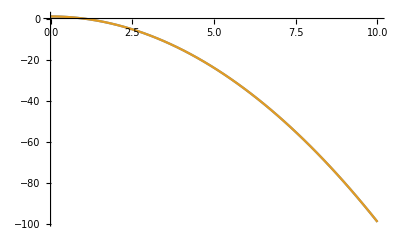

```mathematica
{funTest[1,1,1,1,x],funLeg[1,1,1,1,x]}//Plot[#, {x,0,10}]&//Quiet
```

## 3-J inequalities

Physical Conditions

( j_1 | j_2 | j_3
m_1 | m_2 | m_3 )

```mathematica
ThreeJSymbol[{j1, m1},{j2, m2},{j3, m3}]//.{
j1:>1,j2:>1,j3:>2,m1:>1,m2:>1,m3:>-5
}
```

ClebschGordan::phy: ThreeJSymbol[{1,1},{1,1},{2,-5}] is not physical.

0

```mathematica
W[j1,j2,j3,m1,m2,m3]//.{
j1:>1,j2:>1,j3:>2,m1:>1,m2:>1,m3:>-5
}
```

0